1000

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.18093×10^6 | 186420. | 22.4275 | 8.90979×10^-12
b | 1.15406×10^7 | 359960. | 32.0607 | 9.2574×10^-14

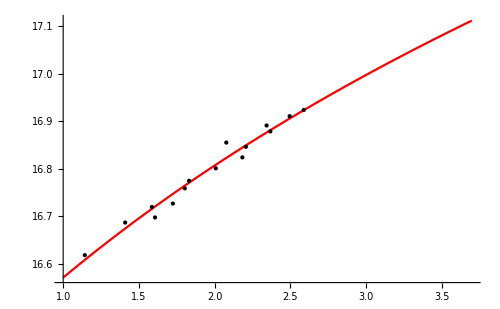

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola_ready_0,25.dat"];
L=Length[data];
Ie=1000
(*Ref = 12*)
Ip[R_]:=a*R+b
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Log[Ip[R]],{a,b},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,0,3.7},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```